```mathematica
H=3;
Nt=10;
Clear[H,Nt]
Assuming[{H>0,Nt>0,H<Nt},∫_0^1 p^2*p^H*(1-p)^(Nt-H)ⅆp]
```

(Gamma[3+H] Gamma[1-H+Nt])/Gamma[4+Nt]

```mathematica
Assuming[{H>0,Nt>0,H<Nt},(∫_0^1 p^2*p^H*(1-p)^(Nt-H)ⅆp)/(∫_0^1 p^H*(1-p)^(Nt-H)ⅆp)]
```

(Gamma[3+H] Gamma[2+Nt])/(Gamma[1+H] Gamma[4+Nt])

```mathematica
FullSimplify[(Gamma[3+H] Gamma[2+Nt])/(Gamma[1+H] Gamma[4+Nt])]
```

((1+H) (2+H))/((2+Nt) (3+Nt))

```mathematica
Assuming[{H>0,Nt>0,H<Nt},((∫_0^1 p*p^H*(1-p)^(Nt-H)ⅆp)/(∫_0^1 p^H*(1-p)^(Nt-H)ⅆp))^2]
```

(Gamma[2+H]^2 Gamma[2+Nt]^2)/(Gamma[1+H]^2 Gamma[3+Nt]^2)

```mathematica
FullSimplify[(Gamma[2+H]^2 Gamma[2+Nt]^2)/(Gamma[1+H]^2 Gamma[3+Nt]^2)]
```

(1+H)^2/(2+Nt)^2

```mathematica
Simplify[((1+H) (2+H))/((2+Nt) (3+Nt))-(1+H)^2/(2+Nt)^2]
```

(1-H^2+Nt+H Nt)/((2+Nt)^2 (3+Nt))

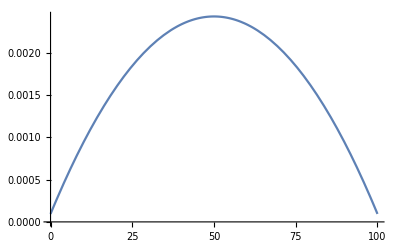

```mathematica
Nt=100;
Plot[(1-H^2+Nt+H Nt)/((2+Nt)^2 (3+Nt)),{H,0,100}]
Clear[H, Nt]
```

```mathematica
Assuming[{H>0,Nt>0,H<Nt},((∫_0^1 p*p^H*(1-p)^(Nt-H)ⅆp)/(∫_0^1 p^H*(1-p)^(Nt-H)ⅆp))]
```

(Gamma[2+H] Gamma[2+Nt])/(Gamma[1+H] Gamma[3+Nt])

```mathematica
FullSimplify[(Gamma[2+H] Gamma[2+Nt])/(Gamma[1+H] Gamma[3+Nt])]
```

(1+H)/(2+Nt)

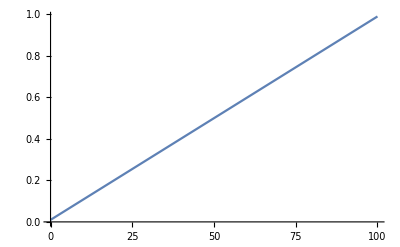

```mathematica
Nt=100;
Plot[(Gamma[2+H] Gamma[2+Nt])/(Gamma[1+H] Gamma[3+Nt]),{H,0,100}]
Clear[Nt]
```